## Goal

Given any input state, classify it into:

- dies out
- contains multiple solutions
- periodic without shift
- periodic with shift s
- aperiodic (e.g. glider gun)

The DetectPeriod[list] function, when given an initial state, returns an association with the period, canonical representation (i.e. smallest reachable state that gives that same solution), and shift.

## Implementation

### Helper Functions

```mathematica
On[Assert];
```

```mathematica
CloseKernels[];
LaunchKernels[];
```

#### Rule Analysis

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule, init, 1][[2,(Length[init]+1)/2]]
```

```mathematica
AnalyzeRule[{n_, {k_, 1}, r_}]:=AnalyzeRule[{n, {k, 1}, r}]=Module[{rule={n, {k, 1}, r},minimumtolerablegap=2r+1},
While[AllTrue[Tuples[Range[k]-1, 2r+2-minimumtolerablegap], PointApplyRule[rule, PadLeft[#, 2r+1]]==0&], minimumtolerablegap--];
<|"Rule"->rule, "Colors"->k, "Totalistic"->True, "Number"->n, "Radius"->r, "MinimumTolerableGap"->minimumtolerablegap|>
]
AnalyzeRule[{n_, k_, r_}]:=AnalyzeRule[{n, k, r}]=Module[{rule={n,k, r},minimumtolerablegap=2r+1},
While[AllTrue[Tuples[{0, 1}, 2r+2-minimumtolerablegap], PointApplyRule[rule, PadLeft[#, 2r+1]]==0&], minimumtolerablegap--];
<|"Rule"->rule, "Colors"->k, "Totalistic"->True, "Number"->n,"Radius"->r, "MinimumTolerableGap"->minimumtolerablegap|>
]
AnalyzeRule[{n_, k_}]:=AnalyzeRule[{n, k, 1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n, 2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]

Timing[AnalyzeRule[{20, {2, 1}, 2}]]
AnalyzeRule[{2, {2, 1}, 2}]
AnalyzeRule[{32, {2, 1}, 2}]
AnalyzeRule[{1329,{3,1},1}]
AnalyzeRule[30]
RepeatedTiming[AnalyzeRule[{20, {2, 1}, 2}]]
```

{0.000406,<|Rule→{20,{2,1},2},Colors→2,Totalistic→True,Number→20,Radius→2,MinimumTolerableGap→4|>}

<|Rule→{2,{2,1},2},Colors→2,Totalistic→True,Number→2,Radius→2,MinimumTolerableGap→5|>

<|Rule→{32,{2,1},2},Colors→2,Totalistic→True,Number→32,Radius→2,MinimumTolerableGap→1|>

<|Rule→{1329,{3,1},1},Colors→3,Totalistic→True,Number→1329,Radius→1,MinimumTolerableGap→3|>

<|Rule→{30,2,1},Colors→2,Totalistic→True,Number→30,Radius→1,MinimumTolerableGap→3|>

{7.55877×10^-8,<|Rule→{20,{2,1},2},Colors→2,Totalistic→True,Number→20,Radius→2,MinimumTolerableGap→4|>}

#### General

```mathematica
AllZeros=FunctionCompile[Function[Typed[list,"PackedArray"::["MachineInteger", 1]], Module[{i=Length[list]}, While[i>0&&list[[i]]==0, i--;]; i==0]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[AllZeros[{0, 0, 0, 0, 1, 0}]]
RepeatedTiming[Max[{0, 0, 0, 0, 1, 0}]==0]
```

{1.64381×10^-7,False}

{1.81789×10^-7,False}

```mathematica
StripZeros=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list]},
If[
(* AllZeros *)
Module[{i0=Length[list]}, While[i0>0&&list[[i0]]==0, i0--;]; i0==0],
 Return[Table[0, {iter, 0}]]
];
While[list[[i]]==0, i++];
 While[list[[j]]==0, j--]; 
list[[i;;j]]
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];

RepeatedTiming[StripZeros[RandomInteger[{0, 1}, 1000]]]//First
StripZeros[{0, 0, 0, 0,0}]
```

1.54396×10^-6

{}

```mathematica
MaxGapLength=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{currentlen=0, maxlen=0},
Do[currentlen=If[i==0, currentlen+1,0]; 
maxlen=Max[maxlen, currentlen];, {i,list}];
maxlen
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[MaxGapLength[RandomInteger[{0, 1}, 1000]]]
```

{4.58709×10^-6,10}

```mathematica
FindRepeatDeterministic[list_List]:=
list[[-First[FirstPosition[Reverse[list[[;;-2]]], list[[-1]], {0}]];;]]

RepeatedTiming[FindRepeatDeterministic[]]//First
```

0.000599141

```mathematica
FindRepeatDeterministicIndexByStripZerosCompiled=FunctionCompile[Function[Typed[list,"PackedArray"::["MachineInteger", 2]],
With[{StripZeros=Function[Typed[list2, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list2]},
While[list2[[i]]==0&&i<j, i++];
 If[i<j,While[list2[[j]]==0, j--]]; 
If[i==j,Table[0, 0],list2[[i;;j]]]]
]},
Module[{i=Length[list]-1, last=StripZeros[list[[-1]]]},
 While[i>0&&StripZeros[list[[i]]]!=last, i--]; If[i==0, 0,i+1]
]]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3}];

FindRepeatDeterministicByStripZeros[list_List]:=StripZeros/@list[[FindRepeatDeterministicIndexByStripZerosCompiled[list];;]]

RepeatedTiming[FindRepeatDeterministicByStripZeros[]]//First
RepeatedTiming[FindRepeatDeterministic[StripZeros/@]]//First
Assert[FindRepeatDeterministicByStripZeros[]==FindRepeatDeterministic[StripZeros/@]]
```

0.0000565232

0.00335579

```mathematica
DedupSamePass1[associations_, parameter_:"Canonical"]:=Union[associations,SameTest->(#1[parameter]==#2[parameter]&)]

DedupSamePass2[associations_, steps_Integer:300]:=Module[{found=CreateDataStructure["HashSet"], out={}, carun, ra}, Do[
carun=RunCA[soln["Rule"], soln["Canonical"], steps];
carun=StripZeros/@carun;
carun=Union[carun];
ra=AnalyzeRule[soln["Rule"]];
If[AllTrue[carun, found["Insert", FromDigits[StripZeros[#], ra["Colors"]]]&], AppendTo[out, soln]]
, {soln, associations}]; out]

DedupSame[associations_, parameter_String:"Canonical", steps_Integer:300]:=SortBy[SortBy[DedupSamePass2[DedupSamePass1[associations, parameter], steps], #Canonical&], #Period&]
```

#### DetectPeriod Subroutines

```mathematica
RunCA[rule_, init_List, steps_]:=CellularAutomaton[rule, {init, 0}, steps]
RunCA[rule_, init_Integer, steps_]:=RunCA[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], steps]

code20rule={20, {2, 1}, 2};
RunCode20[init_, steps_]:=RunCA[code20rule, init, steps]

code1329rule={1329,{3,1},1};
RunCode1329[init_, steps_]:=RunCA[code1329rule, init, steps]
```

```mathematica
Clear[SplitSeparateSolutions];
data={};
SplitSeparateSolutions[carun_, mtg_]:=Module[{mask, mc, colors, carunpadded},
AppendTo[data, carun];
carunpadded=PadLeft[carun, {Length[carun], Length[carun[[-1]]]+mtg}];
mask=Sum[carunpadded[[All,i;;(i-mtg-1)]], {i, mtg}];
mc=Last[MorphologicalComponents[Image[mask], CornerNeighbors->False]];
colors=Union[mc];
Select[Table[StripZeros[(1-Unitize[c-mc[[2;;]]])*carun[[-1]]], {c, colors}], Not@*AllZeros]
]

SplitSeparateSolutions[RunCode20[IntegerDigits[233 + 2^14 * 151, 2], 100], 4]
SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100], 4]
First@Timing[SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100], 4]]
```

{{1,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,1}}

{{1,0,0,1,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,1,1,1,1}}

0.002472

```mathematica
Clear[SplitSeparateSolutions2];
SplitSeparateSolutions2[carun_, rule_]:=Module[{encounteredNonzero=False, first=First[carun], w,superposition, left, right, result=None},
w=Length[first];
Do[
encounteredNonzero=Or[encounteredNonzero, first[[i]]!=0];
If[encounteredNonzero&&first[[i]]==0,
left=CellularAutomaton[rule, ArrayPad[PadRight[first[[;;i]], w], 2], Length[carun]-1];
right=CellularAutomaton[rule,ArrayPad[PadLeft[first[[i;;]], w], 2], Length[carun]-1];
(* Print[ArrayPlot[left], ArrayPlot[right], ArrayPlot[left+right], ArrayPlot[carun]]; *)

superposition=(left+right)[[All, 3;;-3]];

If[superposition==carun&&!AllZeros[Last[left]]&&!AllZeros[Last[right]], 

result=Join[
{StripZeros[Last[left]]},
SplitSeparateSolutions2[right, rule]
];

Break[];
];

encounteredNonzero=False;
];
,{i, w}];

If[result===None, {StripZeros[Last[carun]]}/.{}->Nothing, result]
]
```

#### Visualization

```mathematica
Clear[AArrayPlot];
AArrayPlot[rule_, init_List, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=ArrayPlot[RunCA[rule, init, steps], {ops}]
AArrayPlot[rule_, init_Integer, args___]:=AArrayPlot[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], args]
AArrayPlot[rule_, init_Association, args___]:=AArrayPlot[rule, init["Original"], args]

AArrayPlot[code20rule, 189, ColorRules->"Colors"]
```

-Graphics-

```mathematica
Clear[VisualizeDetectPeriod];
Clear[MultiVisualizeDetectPeriod];
VisualizeDetectPeriod[rule_, init_, stepsog_:None, ops:OptionsPattern[ArrayPlot]]:=Module[{results, steps},
results=DetectPeriod[rule, init];
steps=If[stepsog===None, Min[1000, Max[results[[All, "MaxSteps"]], 0]], stepsog];

Row[{
Labeled[AArrayPlot[rule, init, steps, {ops}], ClickToCopy["Orig", results]],
Row[
Labeled[
AArrayPlot[rule,#Canonical, 5+(3*#Period/.(0->2*steps)),{Mesh->#Period!=0,ops}],ClickToCopy[
#Period/.(0->"None"), #Canonical]]&
/@DedupSame[results]
]
}]
]
MultiVisualizeDetectPeriod[rule_, inits_, args___]:=Column[ParallelTable[VisualizeDetectPeriod[rule, init, args], {init, inits}]]
```

### Detect Period

```mathematica
Clear[DetectPeriod];
Clear[DetectPeriodSub];
DetectPeriod[rule_, n_Integer, args___]:=DetectPeriod[rule, IntegerDigits[n, AnalyzeRule[rule]["Colors"]], args]
DetectPeriod[rule_, list_List, steps_Integer:200, maxdepth_Integer:20]:=With[{ra=AnalyzeRule[rule]}, {res=DetectPeriodSub[ra, list, steps, maxdepth]},Join[<|"Rule"->rule,"Canonical"->FromDigits[list, ra["Colors"]], "Original"->FromDigits[list, ra["Colors"]], "IsGliderGun"->False, "MaxDepth"->maxdepth-#LowestDepth, "MaxSteps"->steps*(2^(1+maxdepth-#LowestDepth)-1)|>, #]&/@res];

DetectPeriodSub[ra_, list_, steps_, ogmaxdepth_]:=Module[
{carun, frd, separatesolutions, period, canonical, shift, maxdepth},
maxdepth=ogmaxdepth;

Assert[maxdepth>=0];

carun=RunCA[ra["Rule"], list, steps];

(* If it dies, return *);
If[AllZeros[carun[[-1]]], Return[{}]];

(* Detect Periodicity *)
frd=FindRepeatDeterministicByStripZeros[carun];

If[ByteCount[carun]>8000000, maxdepth=Min[maxdepth, 2]];

If[maxdepth<=1,If[Length[frd]==0,
Return[{<|"Period"->0, "IsGliderGun"->True, "LowestDepth"->maxdepth|>}],
Return[{<|"Period"->Length[frd],"Canonical"->Min[Min[FromDigits[#,ra["Colors"]]&/@frd], Min[FromDigits[Reverse[#],ra["Colors"]]&/@frd]], x "LowestDepth"->maxdepth|>}];
]];

(* If unfinished and probably unseparated, recurse with more steps *);
If[Length[frd]==0, 
Return[If[MaxGapLength[carun[[-1]]]>15,
separatesolutions=SplitSeparateSolutions2[carun, ra["Rule"]];
Join@@Table[
DetectPeriodSub[ra, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
],
DetectPeriodSub[ra, carun[[-1]], 2 * steps, maxdepth - 1]
]]
];

(* Otherwise, run again for pure periodicity *)
carun=RunCA[ra["Rule"], carun[[-1]], steps];

(* If it's multiperiodic, split solutions *);
separatesolutions=SplitSeparateSolutions2[RunCA[ra["Rule"], carun[[-Length[frd]]], 2*Length[frd]], ra["Rule"]];
(*separatesolutions= SortBy[separatesolutions,First[FirstPosition[#, 1, 0]]&] *);

(* Recurse on each subsolution, if they exist *);
If[Length[separatesolutions]>1,
Return[Join@@Table[
DetectPeriodSub[ra, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
]]
];

(* Return single-solution period *);
period=Length[frd];
canonical=Min[Min[FromDigits[#,ra["Colors"]]&/@frd], Min[FromDigits[Reverse[#],ra["Colors"]]&/@frd]];
carun=RunCA[ra["Rule"],IntegerDigits[canonical, ra["Colors"]], period];
shift=Log[ra["Colors"],FromDigits[First[carun], ra["Colors"]]/FromDigits[Last[carun], ra["Colors"]]];

Return[{<|"Period"->period,"Canonical"->canonical, "Shift"->shift, "LowestDepth"->maxdepth|>}];
]
```

```mathematica
VisualizeDetectPeriod[code20rule, 23126203]
```

-Graphics--Graphics-

```mathematica
VisualizeDetectPeriod[code1329rule, 203640814267187110250933629072365792658504616995457895022364864671272641439998688892001387640731,1200]
```

-Graphics--Graphics--Graphics-

```mathematica
VisualizeDetectPeriod[code20rule,RandomInteger[1, 1000], ImageSize->{200, 200}]
```

-Graphics--Graphics--Graphics-

```mathematica
RepeatedTiming[DetectPeriod[code20rule, RandomInteger[1, 100]];, 3]
RepeatedTiming[DetectPeriod[code1329rule, RandomInteger[2, 100]];, 3]
```

{0.000565417,Null}

{0.0310769,Null}

```mathematica
RepeatedTiming[DetectPeriod[code20rule, #]&/@;, 3]
```

{0.505177,Null}

```mathematica
DetectPeriod[code20rule, 189]
```

{<|Rule→{20,{2,1},2},Canonical→189,Original→189,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→0,LowestDepth→20|>}

## Unit Tests

```mathematica
DetectPeriodTests[testInputs_, printPassing_:True]:=(Do[
Module[{rule, init, eval, err, d, timing, res},
If[i===Null, Continue[]];

rule=i[[1]]; init=i[[2]]; eval=i[[3]];
timing=First[AbsoluteTiming[err=Quiet@Check[d=DetectPeriod[rule, init]; res=eval[d]; False, True]]]; 

avgTiming=((passedTests+failedTests)*avgTiming+timing)/(passedTests+failedTests+1);
AppendTo[allTimings, timing];
If[err, AppendTo[badTestInputs, {rule, init, eval, "Errored"}];Break[]];

If[timing>2 avgTiming&&printPassing, AppendTo[badTestInputs, {rule, init, eval, "Took Too long"}]];

If[res,
passedTests++;
If[printPassing,Print["Passed: ", VisualizeDetectPeriod[rule, init]]];,
failedTests++;
Print["Failed: ", VisualizeDetectPeriod[rule, init, 100]];
AppendTo[badTestInputs, {rule, init, eval, "Failed Test"}]
];
], {i, testInputs}];

Echo["- - - - - Bad Test Cases - - - - -"];

Do[Module[{rule, init, eval, reason},
rule=i[[1]]; init=i[[2]]; eval=i[[3]]; reason=i[[4]];
Print[reason, ": ", VisualizeDetectPeriod[rule, init, 100, Mesh->True, ImageSize->{Automatic, 200}]]
], {i, badTestInputs}];

Print["Passed ", passedTests,"/", passedTests+failedTests, " (", N[100 passedTests/(passedTests+failedTests)],"%), Time Taken (Min/Med/Mean/Max): (",Min[allTimings], "/", Median[allTimings], "/", Mean[allTimings], "/", Max[allTimings], ")", Histogram[allTimings, 100,  ImageSize->Small]]
)
```

#### Main Tests

```mathematica
code20rule={20, {2, 1}, 2};
code1329rule={1329, {3, 1}, 1};
```

- - - - - Bad Test Cases - - - - -

Errored: VisualizeDetectPeriod[{20,{2,1},2},189,100,Mesh→True,ImageSize→{Automatic,200}]

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

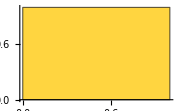
Passed 0/0 (Indeterminate%), Time Taken (Min/Med/Mean/Max): (0.000023/0.000023/0.000023/0.000023)-Graphics-

```mathematica
passedTests=0;failedTests=0;badTestInputs={};avgTiming=0;allTimings={};

testInputs={
{code20rule, 189, #[[1, "Period"]]==1&&#[[1, "Canonical"]]==189&},
{code20rule, 151, #[[1, "Period"]]==2&},
{code20rule, 187, #[[1, "Period"]]==9&},

{code20rule, 1663707641399530118980411815482221, Length[#]==2&&Length[Union[#]]==1&},
{code20rule, 229131364, Length[#]==2&&Length[Union[#]]==1&},

{code20rule, 10404475, Length[#]==2&&Length[Union[#]]==1&},
{code20rule, 24511099, Length[#]==2&&Length[Union[#]]==2&},
{code20rule, 55515189812230754905562323925615995497545449,Length[#]==2&&Length[Union[#]]==2&},

{code20rule, 7906428080021792008667042771196714139750701,Length[#]==1&&#[[1, "Canonical"]]==189&},
{code20rule, 655206922408770031615898646827940682737805468320293536241207188112368362285544739145129771573621207156166901879247829984995504029446985794571779102452257125208791031138705672297617562213256084255316786703087230255899354655197955608651279371536928840963196633039517130860089590001517372103172795357951,True&},


{code1329rule, 9571, #[[1, "Period"]]==78&&#[[1, "Canonical"]]==9571&},
{code1329rule, 1076975378, #[[1, "Period"]]==31&},
{code1329rule, 3192417282, Length[#]==2&&Length[Union[#]]==1&},

{code1329rule, 8895177681968, Length[#]==2&&Length[Union[#]]==1&},
{code1329rule, 2965061397008, Length[#]==2&&Length[Union[#]]==1&},
{code1329rule, 951892141489, Length[#]==1&&Length[Union[#]]==1&},
{code1329rule, 951892141489, Length[#]==1&&Length[Union[#]]==1&},
{code1329rule, 15416340273823942535580279585347100530421847372, Length[#]==2&},
{code1329rule, 2703133095116984, Length[#]==2&&Length[Union[#]]==1&},
{code1329rule, 54889, AnyTrue[#, #IsGliderGun&]&},

{code1329rule, 97439, Length[#]==1&&#[[1,"IsGliderGun"]]&},

{code1329rule, 37279264339387159915935443648681390999359463809, !AnyTrue[#, #IsGliderGun&]&},
};

DetectPeriodTests[testInputs];
```

```mathematica
Select[badTestInputs, Last[#]=="Failed Test"&]//Column
```

#### Easy Tests

```mathematica
Assert[(Sort[DetectPeriod[code20rule, #][[All, "Canonical"]]]&/@)==]
```

#### Random Tests

- - - - - Bad Test Cases - - - - -

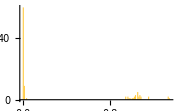
Passed 100/100 (100.%), Time Taken (Min/Med/Mean/Max): (0.00115/0.0060845/0.324199/1.34314)-Graphics-

```mathematica
passedTests=0;failedTests=0;badTestInputs={};avgTiming=0;allTimings={};
randomTestInputs=Table[{code20rule, RandomInteger[2^1000], True&}, 100];
DetectPeriodTests[randomTestInputs, False];
```

```mathematica
badTestInputs
```

{}

```mathematica
passedTests=0;failedTests=0;badTestInputs={};avgTiming=0;allTimings={};
randomTestInputs=Table[{code1329rule, RandomInteger[3^1000], True&}, 100];
DetectPeriodTests[randomTestInputs, False];
```

$Aborted

```mathematica
0.00428, 0.009
0.11269
```

```mathematica
"("0.071083"/"0.11269"/"0.11261020999999996"/"0.180709
```

## Manual Testing

```mathematica
DedupSame[Join@@ParallelTable[DetectPeriod[{52, {2, 1}, 2}, i], {i, 0, 10000}]]
```

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
MultiVisualizeDetectPeriod[{52, {2, 1}, 2},[[All, "Canonical"]]]
```

Can we find a solution to

```mathematica
IntegerDigits[52, 2]
```

{1,1,0,1,0,0}

```mathematica
VisualizeDetectPeriod[{52, {2,1}, 2}, #]&/@{55, 59, 110, 111, 118, 6291453, 25165821, 41943035, 100663293, 151, 189, 635}
```

{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
rule110
```

rule110

```mathematica
ArrayPlot[CellularAutomaton[110, RandomInteger[1, 1000], 1000]]
```

-Graphics-

```mathematica
https://vixra.org/abs/2601.0001
```

```mathematica
ParallelTable[Labeled[ArrayPlot[CellularAutomaton[{i, {2, 1}, 2}, {RandomInteger[1, 100], 0}, 100]], i], {i, 0, 63, 2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[Labeled[ArrayPlot[CellularAutomaton[{i, {2, 1}, 2}, {RandomInteger[1, 100], 0}, 1000]], i], {i,{20, 52, 48, 40, 36, 32, 16, 8, 4, 12, 44}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Join@@ParallelTable[DetectPeriod[{36, {2, 1}, 2}, i], {i, 2000001, 3000000, 2}]
```

{}

```mathematica
Join@@%
```

{}

```mathematica
Join@@ParallelTable[DetectPeriod[{40, {2, 1}, 2}, i], {i, 200001, 400000, 2}]
```

```mathematica
DedupSame[%]
```

{<|Rule→{40,{2,1},2},Canonical→7,Original→200001,IsGliderGun→False,MaxDepth→0,MaxSteps→200,Period→1,Shift→0,LowestDepth→20|>}

```mathematica
Join@@ParallelTable[DetectPeriod[{36, {2, 1}, 2}, i], {i, 4000001, 6000000, 2}]
```

{}

```mathematica
Join@@ParallelTable[DetectPeriod[{36, {2, 1}, 2}, i], {i, 6000001, 8000000, 2}]
```

```mathematica
Join@@ParallelTable[DetectPeriod[{36, {2, 1}, 2}, i], {i, 8000001, 10000000, 2}]
```

```mathematica
DedupSame[Join@@ParallelTable[DetectPeriod[{40, {2, 1}, 2}, StripZeros@RandomInteger[1, 1000]], {i,100000}]][[All, "Canonical"]]
```

{7}

```mathematica
ParallelTable[Labeled[ArrayPlot[CellularAutomaton[{12, {2, 1}, 2}, {C, 0}, 100], ImageSize->{1000, 200}], i], {i, RandomInteger[50, {20, 20}]}]//Column
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

General::stop: Further output of The current computation was aborted because there was insufficient memory available to complete the computation. will be suppressed during this calculation.

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

ArrayPlot::mat: Argument … at position 1 is not a list of lists.

LinkRead::time: Operation LinkRead timed out after 3. seconds.

KernelObject::rdead: Discarding kernel 1 (Local).

LinkRead::time: Operation LinkRead timed out after 3. seconds.

KernelObject::rdead: Discarding kernel 3 (Local).

LinkRead::time: Operation LinkRead timed out after 3. seconds.

```mathematica
ArrayPlot[CellularAutomaton[{12, {2, 1}, 2}, {, 0}, 2000]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{12, {2, 1}, 2}, {, 0}, 2000]]
```

-Graphics-

```mathematica
DedupSame[DetectPeriod[{1772277832,2,2}, 3637115]]
```

{<|Rule→{1772277832,2,2},Canonical→223,Original→3637115,IsGliderGun→False,MaxDepth→2,MaxSteps→1400,Period→3,Shift→-3,LowestDepth→18|>}